## 計算結果

```mathematica
Clear["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../mathematica_utilities/mathematica_plot_options.nb"}]]
(*json="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.json"*)
(*json ="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water_no_float0d09/result.json"*)
jsonTarget=json="/Volumes/home/BEM/benchmark202405/Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater0d08_DT0d01_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json"
jsonInfo[json]
```

Available:{plot2Doption,plot3Doption,framelabel[xlabel_String,ylabel_String,size_:20],axeslabel2D[xlabel_String,ylabel_String,size_:20],axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20],axeslabel[labels_List,size_: 20],importData,jsonInfo,interpolateAndFourier,interpolateAndFourierTr,getOmegaFromKandDepth,getTFromLandDepth}

/Volumes/home/BEM/benchmark202405/Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater0d08_DT0d01_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json

no. | title | length
1 | cpu_time | 91
2 | eq_of_motion | 91
3 | float_COM | 91
4 | float_EK | 91
5 | float_EP | 91
6 | float_accel | 91
7 | float_area | 91
8 | float_drag_force | 91
9 | float_drag_torque | 91
10 | float_force | 91
11 | float_pitch | 91
12 | float_roll | 91
13 | float_torque | 91
14 | float_velocity | 91
15 | float_yaw | 91
16 | gauge0_intersection | 91
17 | gauge10_intersection | 91
18 | gauge11_intersection | 91
19 | gauge12_intersection | 91
20 | gauge13_intersection | 91
21 | gauge14_intersection | 91
22 | gauge15_intersection | 91
23 | gauge16_intersection | 91
24 | gauge17_intersection | 91
25 | gauge18_intersection | 91
26 | gauge19_intersection | 91
27 | gauge1_intersection | 91
28 | gauge20_intersection | 91
29 | gauge21_intersection | 91
30 | gauge22_intersection | 91
31 | gauge23_intersection | 91
32 | gauge2_intersection | 91
33 | gauge3_intersection | 91
34 | gauge4_intersection | 91
35 | gauge5_intersection | 91
36 | gauge6_intersection | 91
37 | gauge7_intersection | 91
38 | gauge8_intersection | 91
39 | gauge9_intersection | 91
40 | gradPhi_worst_grad | 91
41 | gradPhi_worst_iteration | 91
42 | gradPhi_worst_value | 91
43 | simulation_time | 91
44 | wall_clock_time | 91
45 | water_E | 91
46 | water_EK | 91
47 | water_EP | 91
48 | water_face_size | 91
49 | water_point_size | 91
50 | water_volume | 91

```mathematica
(*i=1;
ListPlot[
Table[With[{name="float"<>ToString[i]<>"_COM"},importData[json,name,1]-importData[json,name,1][[1]]],{i,1,20,1}]
,Joined->True
]
ListPlot[
Table[With[{name="float"<>ToString[i]<>"_COM"},importData[json,name,2]-importData[json,name,2][[1]]],{i,1,20,1}]
,Joined->True
]
ListPlot[
Table[With[{name="float"<>ToString[i]<>"_COM"},importData[json,name,3]-importData[json,name,3][[1]]],{i,1,20,1}]
,Joined->True
]*)
```

```mathematica
(*Tshift=6.5*)
Tshift=-7.55

ExpHeave={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_heave_exp.csv"];
SimuHeave={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_heave_simu.csv"];
ExpSway={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_sway_exp.csv"];
SimuSway={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_sway_simu.csv"];
ExpRoll={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_roll_exp.csv"];
SimuRoll={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_roll_simu.csv"];
ExpSf={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_Sf_exp.csv"];
SimuSf={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_Sf_simu.csv"];
SimuRm={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_Rm_simu.csv"];
SimuHf={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_Hf_simu.csv"];
```

-7.55

```mathematica
ζa=0.05/2;
{B,L}={0.74,0.997};(*{Bredth,Length}*)
g=9.8;
ρ=1000;
λ=1.8;
ρgLBζa=ρ*g*L*B*ζa

h=5.;
Omega[k_,h_]:=Sqrt[g*k*Tanh[h*k]];
Tw=T/.Solve[Omega[2π/λ,h]==2π/T,T][[1]];

k=2π/L;
ω=Omega[k,h];
```

180.756

Solve::ratnz: Solveは厳密でない係数の系を解くことができませんでした．解は対応する厳密系を解き，結果を数値に変換することで得られました．

## 計算結果

```mathematica
fourColorScheme={
{Thick,Opacity[0.8],Blue(*RGBColor[55/255,126/255,184/255]*)},
{Thickness[0.002],Opacity[0.8],Red(*RGBColor[255/255,127/255,0]*)},
{Thickness[0.002],RGBColor[77/255,175/255,74/255]},
{Thickness[0.002],RGBColor[247/255,129/255,191/255]}};
threeColorScheme={{Thick,RGBColor[55/255,126/255,184/255]},RGBColor[255/255,127/255,0],RGBColor[77/255,175/255,74/255]};
plotxrange={{0,30},All};
opt={FrameStyle->Directive[FontSize->16,Black,Thickness[0.002]],
Epilog->{Line[{{-100,0},{100,0}}]},
Joined->{True,True,True,False},
PlotRange->plotxrange,
GridLines->All,
GridLinesStyle->Directive[Gray,AbsoluteThickness[0.001]],
ImageSize->1000,
(*PlotStyle->{{Blue},{Red},{Darker[Green]}},*)
PlotStyle->fourColorScheme,
AspectRatio->1/8};
(*メッシュと計算の収束*)
```

```mathematica
simutime=importData[json,"simulation_time"]/Tw;
```

```mathematica
(*プロット*)
Column@Table[
ListLogPlot[Transpose[{Range[Length[#]],#}]&@@@importData[json,"eq_of_motion"][[;;100]],
PlotLabel->json,
PlotRange->Automatic,
PlotStyle->Directive[Thin,Black,Opacity[0.2]],
FrameTicks->{{All,Automatic},{Table[i,{i,1,100,1}],None}},
AspectRatio->1/2,
FrameLabel->{
Style["Number of evaluations",FontSize->20,FontFamily->"Times"],
Rotate[Style["error |Q|",FontSize->20,FontFamily->"Times"],-π/2]},
Frame->True,
Evaluate[plot2Doption]
],{json,
{json=jsonTarget(*,
"/Volumes/home/BEM/20240301土木学会東北支部/Tanizawa1996_H0d05_L1d8_potential_multiple_water_mod_coarse/result.json"*)}}]
```

Part::take: {{{3.49622×10^-6,4.14029×10^-6,3.9325×10^-6,0.0000185489,9.09639×10^-9,2.04543×10^-8,3.03983×10^-13}},{{0.000236483,0.000282513,0.000248113,0.00110641,6.63619×10^-7,1.49241×10^-6,1.3167×10^-13}},{{0.000165688,0.000208894,4.40546×10^-6,0.0000100382,1.27102×10^-7,2.85325×10^-7,4.32396×10^-13}},«45»,{{21302.8,26845.1,1788.56,4103.05,19.5294,43.8305,8.53029×10^-9,5.94788×10^-10,7.86315×10^-11}},{{3971.95,5007.86,57.2532,130.385,0.459568,1.03166,1.77328×10^-9,1.87355×10^-10,2.10501×10^-10,2.60274×10^-10,1.1553×10^-10,1.51366×10^-10,4.6182×10^-11}},«41»}の1から100の位置が取れません．

Transpose::nmtx: {{},1}の最初の2個のレベルは転置できません．

Part::pkspec1: 式Transpose[{{},1}]は部分指定に使用できません．

General::stop: この計算中に，Part::pkspec1のこれ以上の出力は表示されません．

ListLogPlot::lpn: {{1.,{3.49622×10^-6,4.14029×10^-6,3.9325×10^-6,0.0000185489,9.09639×10^-9,2.04543×10^-8,3.03983×10^-13}}}⟦Transpose[{{},1}]⟧は数値のリストあるいは数値の対のリストではありません．

General::stop: この計算中に，ListLogPlot::lpnのこれ以上の出力は表示されません．

ListLogPlot[{{1,{3.49622×10^-6,4.14029×10^-6,3.9325×10^-6,0.0000185489,9.09639×10^-9,2.04543×10^-8,3.03983×10^-13}}}⟦Transpose[{{},1}]⟧,PlotLabel→/Volumes/home/BEM/benchmark202405/Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater0d08_DT0d01_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json,PlotRange→Automatic,PlotStyle→Directive[Thickness[Tiny],GrayLevel[0],Opacity[0.2]],FrameTicks→{{All,Automatic},{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},None}},AspectRatio→1/2,FrameLabel→{Number of evaluations,error |Q|},Frame→True,{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]

この計算条件では，準ニュートン法の繰り返し計算7回で | Q | < 10^-12 にまで収束した．
浮体を増やすと，収束の速さは遅くなるものの収束する．

```mathematica
opt=Append[opt,{PlotStyle->plotstyle,
PlotRange->{All,Automatic},
PlotLegends->{"Present","Tanizawa 1997","Experiment"}}];
```

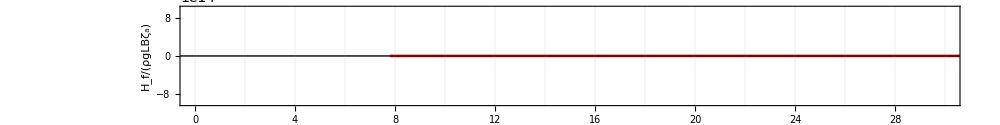

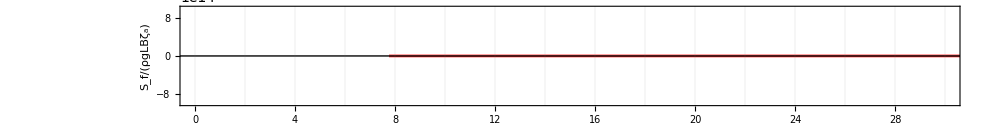

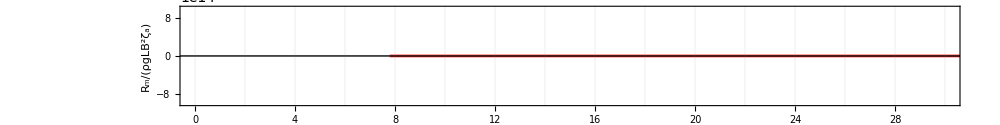

ListPlot::lpn: {{},{{0.,0.0126615},{0.0502001,0.00183025},{0.1004,0.0023423},{0.1506,0.00775449},{0.200801,0.00298018},{0.251001,0.00613242},{0.301201,0.0109158},{0.351401,0.0100242},«36»,{2.20881,0.00590655},{2.25901,0.00607736},{2.30921,0.00177069},{2.35941,0.00241249},{2.40961,0.00813904},{2.45981,0.00484024},«212»}}は数値のリストあるいは数値の対のリストではありません．

General::stop: この計算中に，ListPlot::lpnのこれ以上の出力は表示されません．

ListPlot[{{},{{0.,0.0126615},{0.0502001,0.00183025},{0.1004,0.0023423},{0.1506,0.00775449},{0.200801,0.00298018},{0.251001,0.00613242},{0.301201,0.0109158},{0.351401,0.0100242},{0.401601,0.00387457},{0.451801,0.0106189},{0.502001,0.00801694},{0.552202,0.00691184},{0.602402,0.0131494},{0.652602,0.0158759},{0.702802,0.0104053},{0.753002,0.0176497},{0.803202,0.0150446},{0.853402,0.0173972},{0.903603,0.030605},{0.953803,0.0487533},{1.004,0.213162},{1.0542,0.0221017},{1.1044,0.016733},{1.1546,0.0104887},{1.2048,0.00790696},{1.255,0.00983967},{1.3052,0.00895408},{1.3554,0.00837115},{1.4056,0.0105876},{1.4558,0.0129797},{1.506,0.0110208},{1.5562,0.00852263},{1.6064,0.00677192},{1.6566,0.00196376},{1.7068,0.00424611},{1.75701,0.00713805},{1.80721,0.00618219},{1.85741,0.00395604},{1.90761,0.00724936},{1.95781,0.0105814},{2.00801,0.0334456},{2.05821,0.0047654},{2.10841,0.0109796},{2.15861,0.00602826},{2.20881,0.00590655},{2.25901,0.00607736},{2.30921,0.00177069},{2.35941,0.00241249},{2.40961,0.00813904},{2.45981,0.00484024},{2.51001,0.00529671},{2.56021,0.00475433},{2.61041,0.00619329},{2.66061,0.00372342},{2.71081,0.00681956},{2.76101,0.00575537},{2.81121,0.00376179},{2.86141,0.00566329},{2.91161,0.00884346},{2.96181,0.00699705},{3.01201,0.00666731},{3.06221,0.00477765},{3.11241,0.0016242},{3.16261,0.0057534},{3.21281,0.00649305},{3.26301,0.00581887},{3.31321,0.0046138},{3.36341,0.00545435},{3.41361,0.00623159},{3.46381,0.00299173},{3.51401,0.00905898},{3.56421,0.00601456},{3.61441,0.00211755},{3.66461,0.00589666},{3.71481,0.0023159},{3.76501,0.00532677},{3.81521,0.00763731},{3.86541,0.00728319},{3.91561,0.00192144},{3.96581,0.00515179},{4.01601,0.00282233},{4.06621,0.00170203},{4.11641,0.00265439},{4.16661,0.000823804},{4.21681,0.00369994},{4.26701,0.00242641},{4.31721,0.00775429},{4.36741,0.00629635},{4.41761,0.00258675},{4.46781,0.00296377},{4.51801,0.00546017},{4.56821,0.00150021},{4.61841,0.00637646},{4.66861,0.0104609},{4.71881,0.00277005},{4.76901,0.00472958},{4.81921,0.00383671},{4.86941,0.00371585},{4.91961,0.00299744},{4.96981,0.00116667},{5.02001,0.00582479},{5.07021,0.00434139},{5.12041,0.00365702},{5.17062,0.00124893},{5.22082,0.00283528},{5.27102,0.00218221},{5.32122,0.0056182},{5.37142,0.00364633},{5.42162,0.00419323},{5.47182,0.00526149},{5.52202,0.00341667},{5.57222,0.00600744},{5.62242,0.00308155},{5.67262,0.00206991},{5.72282,0.00590215},{5.77302,0.00312457},{5.82322,0.00390261},{5.87342,0.00222576},{5.92362,0.00303447},{5.97382,0.00274452},{6.02402,0.000650857},{6.07422,0.00179229},{6.12442,0.00593121},{6.17462,0.00253613},{6.22482,0.00261612},{6.27502,0.00234897},{6.32522,0.00525342},{6.37542,0.00150041},{6.42562,0.00558306},{6.47582,0.00300851},{6.52602,0.00127514},{6.57622,0.00576422},{6.62642,0.00280912},{6.67662,0.00373725},{6.72682,0.00506043},{6.77702,0.00224112},{6.82722,0.00487348},{6.87742,0.00394453},{6.92762,0.00294849},{6.97782,0.00318041},{7.02802,0.00429912},{7.07822,0.00105656},{7.12842,0.00106756},{7.17862,0.00505105},{7.22882,0.00382786},{7.27902,0.00323962},{7.32922,0.0018992},{7.37942,0.00330621},{7.42962,0.00426078},{7.47982,0.00253969},{7.53002,0.00285069},{7.58022,0.0025481},{7.63042,0.000875554},{7.68062,0.00479512},{7.73082,0.00348627},{7.78102,0.00328709},{7.83122,0.00488145},{7.88142,0.003552},{7.93162,0.00264782},{7.98182,0.00613637},{8.03202,0.00657925},{8.08222,0.00429316},{8.13242,0.00466929},{8.18262,0.00334489},{8.23282,0.00181929},{8.28302,0.00191901},{8.33322,0.00323659},{8.38342,0.00578702},{8.43362,0.00249402},{8.48382,0.00499888},{8.53402,0.00182511},{8.58423,0.00425641},{8.63443,0.00306389},{8.68463,0.00387317},{8.73483,0.00308936},{8.78503,0.00289165},{8.83523,0.00682333},{8.88543,0.00106735},{8.93563,0.00514792},{8.98583,0.00566294},{9.03603,0.00343603},{9.08623,0.00407463},{9.13643,0.00452242},{9.18663,0.00261769},{9.23683,0.00164108},{9.28703,0.00322777},{9.33723,0.00261134},{9.38743,0.00176101},{9.43763,0.00480596},{9.48783,0.00333534},{9.53803,0.00288797},{9.58823,0.000232516},{9.63843,0.00547175},{9.68863,0.000238775},{9.73883,0.0040418},{9.78903,0.00240102},{9.83923,0.00752816},{9.88943,0.00300107},{9.93963,0.00439113},{9.98983,0.00709106},{10.04,0.00225673},{10.0902,0.00392953},{10.1404,0.0032067},{10.1906,0.00314158},{10.2408,0.00325698},{10.291,0.00427736},{10.3412,0.00463341},{10.3914,0.000975135},{10.4416,0.00320483},{10.4918,0.0035808},{10.542,0.00310295},{10.5922,0.00523968},{10.6424,0.00537586},{10.6926,0.00359019},{10.7428,0.00592262},{10.793,0.00247807},{10.8432,0.00534286},{10.8934,0.00510041},{10.9436,0.00169576},{10.9938,0.00648904},{11.044,0.00526392},{11.0942,0.00436896},{11.1444,0.00673466},{11.1946,0.00558875},{11.2448,0.00335472},{11.295,0.00434498},{11.3452,0.00585462},{11.3954,0.000683323},{11.4456,0.006453},{11.4958,0.00349449},{11.546,0.00691067},{11.5962,0.00429143},{11.6464,0.00602401},{11.6966,0.00385744},{11.7468,0.00529073},{11.797,0.00209132},{11.8472,0.0028427},{11.8974,0.00448694},{11.9476,0.00410756},{11.9978,0.00541596},{12.048,0.00434799},{12.0982,0.00596078},{12.1484,0.004515},{12.1986,0.00683936},{12.2488,0.0028382},{12.299,0.00600915},{12.3492,0.00417554},{12.3994,0.00119447},{12.4496,0.00504577},{12.4998,0.0062987},{12.55,0.00455686},{12.6002,0.0023994},{12.6504,0.00678878},{12.7006,0.00150539},{12.7508,0.00229954},{12.801,0.00522544},{12.8512,0.00699333},{12.9014,0.000968162},{12.9516,0.00487832},{13.0018,0.00659088},{13.052,0.00300647},{13.1022,0.00546427}}},PlotRange→{{0,3},All},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]

ListPlot::lpn: {{},{{0.,0.0148589},{0.0502012,0.0178278},{0.100402,0.00420118},{0.150603,0.0118102},{0.200805,0.00743294},{0.251006,0.0124319},{0.301207,0.0117818},«37»,{2.20885,0.00694352},{2.25905,0.010214},{2.30925,0.00709757},{2.35945,0.0106276},{2.40966,0.0111212},{2.45986,0.00198289},«288»}}は数値のリストあるいは数値の対のリストではありません．

General::stop: この計算中に，ListPlot::lpnのこれ以上の出力は表示されません．

ListPlot[{{},{{0.,0.0148589},{0.0502012,0.0178278},{0.100402,0.00420118},{0.150603,0.0118102},{0.200805,0.00743294},{0.251006,0.0124319},{0.301207,0.0117818},{0.351408,0.0209363},{0.401609,0.00864363},{0.45181,0.00878388},{0.502012,0.0105507},{0.552213,0.0169147},{0.602414,0.00969621},{0.652615,0.0158608},{0.702816,0.0167095},{0.753017,0.0111177},{0.803218,0.0117956},{0.85342,0.0251698},{0.903621,0.0371893},{0.953822,0.0546789},{1.00402,0.222679},{1.05422,0.0344013},{1.10443,0.0170327},{1.15463,0.0203237},{1.20483,0.00706665},{1.25503,0.0116551},{1.30523,0.0170055},{1.35543,0.00748778},{1.40563,0.00676581},{1.45583,0.00917375},{1.50603,0.00877885},{1.55624,0.00929327},{1.60644,0.0108212},{1.65664,0.0186409},{1.70684,0.00889617},{1.75704,0.00337823},{1.80724,0.00403539},{1.85744,0.00305069},{1.90764,0.00931556},{1.95784,0.0173926},{2.00805,0.0215488},{2.05825,0.00927115},{2.10845,0.00634311},{2.15865,0.00703228},{2.20885,0.00694352},{2.25905,0.010214},{2.30925,0.00709757},{2.35945,0.0106276},{2.40966,0.0111212},{2.45986,0.00198289},{2.51006,0.0062175},{2.56026,0.00926786},{2.61046,0.0147579},{2.66066,0.0112401},{2.71086,0.00302518},{2.76106,0.0105662},{2.81126,0.000940407},{2.86147,0.0144845},{2.91167,0.015416},{2.96187,0.0129262},{3.01207,0.00750597},{3.06227,0.00722878},{3.11247,0.000753103},{3.16267,0.000183431},{3.21287,0.0110522},{3.26307,0.000714909},{3.31328,0.00719315},{3.36348,0.00659857},{3.41368,0.00797568},{3.46388,0.00206746},{3.51408,0.0107441},{3.56428,0.00547787},{3.61448,0.0168086},{3.66468,0.010943},{3.71489,0.00247971},{3.76509,0.00522074},{3.81529,0.00794149},{3.86549,0.00453789},{3.91569,0.0128881},{3.96589,0.00991508},{4.01609,0.00153918},{4.06629,0.00510441},{4.11649,0.00861928},{4.1667,0.00686822},{4.2169,0.0127781},{4.2671,0.00716688},{4.3173,0.00479842},{4.3675,0.00501793},{4.4177,0.00496466},{4.4679,0.0038273},{4.5181,0.00633949},{4.5683,0.00754538},{4.61851,0.0178941},{4.66871,0.00359251},{4.71891,0.00930259},{4.76911,0.0131673},{4.81931,0.00154183},{4.86951,0.00640056},{4.91971,0.0115289},{4.96991,0.00226927},{5.02012,0.00465759},{5.07032,0.00845264},{5.12052,0.00733453},{5.17072,0.00504486},{5.22092,0.0136409},{5.27112,0.00743088},{5.32132,0.00809173},{5.37152,0.00481327},{5.42172,0.00699591},{5.47193,0.00460048},{5.52213,0.00432889},{5.57233,0.00933305},{5.62253,0.0105623},{5.67273,0.00510375},{5.72293,0.0023221},{5.77313,0.00773266},{5.82333,0.00703405},{5.87353,0.00403831},{5.92374,0.0102702},{5.97394,0.00699978},{6.02414,0.00724435},{6.07434,0.00686247},{6.12454,0.00231819},{6.17474,0.00650999},{6.22494,0.00812706},{6.27514,0.000158995},{6.32535,0.000693789},{6.37555,0.00717137},{6.42575,0.00820416},{6.47595,0.00539498},{6.52615,0.00653315},{6.57635,0.00256203},{6.62655,0.00961204},{6.67675,0.00854007},{6.72695,0.00233781},{6.77716,0.00760462},{6.82736,0.00155017},{6.87756,0.00436516},{6.92776,0.00402349},{6.97796,0.00485346},{7.02816,0.000966718},{7.07836,0.00691452},{7.12856,0.00642535},{7.17876,0.0046647},{7.22897,0.00952561},{7.27917,0.00235876},{7.32937,0.0061604},{7.37957,0.00145148},{7.42977,0.00519668},{7.47997,0.00473927},{7.53017,0.00548001},{7.58037,0.0047223},{7.63057,0.0034588},{7.68078,0.00934516},{7.73098,0.00205832},{7.78118,0.0062834},{7.83138,0.0033595},{7.88158,0.00401851},{7.93178,0.00801663},{7.98198,0.0106187},{8.03218,0.00863344},{8.08239,0.00579456},{8.13259,0.00344274},{8.18279,0.00735879},{8.23299,0.00824819},{8.28319,0.00701656},{8.33339,0.00879794},{8.38359,0.00724796},{8.43379,0.00522504},{8.48399,0.00490325},{8.5342,0.00286313},{8.5844,0.00846758},{8.6346,0.00138762},{8.6848,0.0138829},{8.735,0.00521653},{8.7852,0.00326241},{8.8354,0.00170884},{8.8856,0.0018238},{8.9358,0.00739072},{8.98601,0.00722729},{9.03621,0.00581213},{9.08641,0.00548227},{9.13661,0.00345479},{9.18681,0.00248129},{9.23701,0.0024177},{9.28721,0.005765},{9.33741,0.0110865},{9.38762,0.0125836},{9.43782,0.00296103},{9.48802,0.00137542},{9.53822,0.00392573},{9.58842,0.00648428},{9.63862,0.0063184},{9.68882,0.00704397},{9.73902,0.00259616},{9.78922,0.00251625},{9.83943,0.000846335},{9.88963,0.00764086},{9.93983,0.0026764},{9.99003,0.0102599},{10.0402,0.00569515},{10.0904,0.00346804},{10.1406,0.00470671},{10.1908,0.00281772},{10.241,0.00488382},{10.2912,0.0119125},{10.3414,0.00790112},{10.3916,0.00822222},{10.4418,0.00436867},{10.492,0.00374481},{10.5422,0.00038999},{10.5924,0.00335066},{10.6426,0.00562919},{10.6928,0.00370586},{10.743,0.00470868},{10.7932,0.00289018},{10.8434,0.00195404},{10.8936,0.00798078},{10.9439,0.00353208},{10.9941,0.00632868},{11.0443,0.00394418},{11.0945,0.00475848},{11.1447,0.00223308},{11.1949,0.00595339},{11.2451,0.00553935},{11.2953,0.00695681},{11.3455,0.00736935},{11.3957,0.00228632},{11.4459,0.00557292},{11.4961,0.00564204},{11.5463,0.00690193},{11.5965,0.00719389},{11.6467,0.00476524},{11.6969,0.000631383},{11.7471,0.0052643},{11.7973,0.00261595},{11.8475,0.00258371},{11.8977,0.00662781},{11.9479,0.0067432},{11.9981,0.00449592},{12.0483,0.00132108},{12.0985,0.00176782},{12.1487,0.00394599},{12.1989,0.00319798},{12.2491,0.00955723},{12.2993,0.000836828},{12.3495,0.00764531},{12.3997,0.00826619},{12.4499,0.00269758},{12.5001,0.00162614},{12.5503,0.00540033},{12.6005,0.00927498},{12.6507,0.0047924},{12.7009,0.00338356},{12.7511,0.00472413},{12.8013,0.0042932},{12.8515,0.0028653},{12.9017,0.00707624},{12.9519,0.00511575},{13.0021,0.00195038},{13.0523,0.00484835},{13.1025,0.00568999},{13.1527,0.00339633},{13.2029,0.0056844},{13.2531,0.00451504},{13.3033,0.0105828},{13.3535,0.00416949},{13.4037,0.00699222},{13.4539,0.00332871},{13.5041,0.00155154},{13.5543,0.00397518},{13.6045,0.00806658},{13.6547,0.00683882},{13.7049,0.00195321},{13.7551,0.000439846},{13.8053,0.00497794},{13.8555,0.00272561},{13.9057,0.00542227},{13.9559,0.00746239},{14.0061,0.00481655},{14.0563,0.0048527},{14.1065,0.000388192},{14.1567,0.00667402},{14.2069,0.00238021},{14.2571,0.0044581},{14.3073,0.00813063},{14.3575,0.00645827},{14.4077,0.00485389},{14.4579,0.00241509},{14.5081,0.00262793},{14.5583,0.00137468},{14.6085,0.00357942},{14.6587,0.0142831},{14.7089,0.00811707},{14.7591,0.00387807},{14.8093,0.00592636},{14.8595,0.00467271},{14.9097,0.00292037},{14.9599,0.00874868},{15.0101,0.00559973},{15.0603,0.00164573},{15.1105,0.00442738},{15.1607,0.00290095},{15.2109,0.0015066},{15.2611,0.0135769},{15.3114,0.00532684},{15.3616,0.00254145},{15.4118,0.00490581},{15.462,0.00805587},{15.5122,0.00464028},{15.5624,0.00237649},{15.6126,0.00373271},{15.6628,0.0137913},{15.713,0.0103255},{15.7632,0.00248544},{15.8134,0.00724933},{15.8636,0.00592547},{15.9138,0.00165371},{15.964,0.00476071},{16.0142,0.00379094},{16.0644,0.00199749},{16.1146,0.00646677},{16.1648,0.00436092},{16.215,0.00491471},{16.2652,0.0207801},{16.3154,0.00322468},{16.3656,0.00100433},{16.4158,0.00531045},{16.466,0.00473319},{16.5162,0.000221666},{16.5664,0.00391081},{16.6166,0.00715412},{16.6668,0.0217095},{16.717,0.0118357},{16.7672,0.00174935},{16.8174,0.00345528},{16.8676,0.00166223},{16.9178,0.00465284}}},PlotRange→{{0,3},All},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]

ListPlot::lpn: {{},{{0.,0.000640236},{0.0500558,0.0000781921},{0.100112,0.00026843},{0.150168,0.000339601},{0.200223,0.00010371},{0.250279,0.000219389},{0.300335,0.000192647},«37»,{2.20246,0.000129591},{2.25251,0.000202778},{2.30257,0.000122728},{2.35262,0.0000721879},{2.40268,0.000328709},{2.45274,0.000086229},«238»}}は数値のリストあるいは数値の対のリストではありません．

General::stop: この計算中に，ListPlot::lpnのこれ以上の出力は表示されません．

ListPlot[{{},{{0.,0.000640236},{0.0500558,0.0000781921},{0.100112,0.00026843},{0.150168,0.000339601},{0.200223,0.00010371},{0.250279,0.000219389},{0.300335,0.000192647},{0.350391,0.000102889},{0.400447,0.00017189},{0.450503,0.000205041},{0.500558,0.000207725},{0.550614,0.000119294},{0.60067,0.000161854},{0.650726,0.0000841088},{0.700782,0.000239592},{0.750838,0.000280093},{0.800893,0.000123902},{0.850949,0.000667865},{0.901005,0.000962687},{0.951061,0.000668998},{1.00112,0.00549722},{1.05117,0.0012618},{1.10123,0.000405379},{1.15128,0.000316587},{1.20134,0.000168337},{1.2514,0.000154743},{1.30145,0.0000814285},{1.35151,0.0000318426},{1.40156,0.000204424},{1.45162,0.000159464},{1.50168,0.0000283558},{1.55173,0.000140198},{1.60179,0.000156441},{1.65184,0.000100844},{1.7019,0.000171752},{1.75195,0.000145378},{1.80201,0.000116035},{1.85207,0.000172482},{1.90212,0.000449095},{1.95218,0.000375715},{2.00223,0.00158011},{2.05229,0.000366696},{2.10235,0.000456588},{2.1524,0.000383655},{2.20246,0.000129591},{2.25251,0.000202778},{2.30257,0.000122728},{2.35262,0.0000721879},{2.40268,0.000328709},{2.45274,0.000086229},{2.50279,0.000122962},{2.55285,0.0000744263},{2.6029,0.000191156},{2.65296,0.000212494},{2.70302,0.000132869},{2.75307,0.000120984},{2.80313,0.0000579548},{2.85318,0.000206059},{2.90324,0.000038342},{2.95329,0.000153558},{3.00335,0.000183636},{3.05341,0.000118667},{3.10346,0.000136303},{3.15352,0.0000708915},{3.20357,0.000129648},{3.25363,0.0000116752},{3.30369,0.000165252},{3.35374,0.0000171454},{3.4038,0.000221004},{3.45385,0.0000820458},{3.50391,0.0000408945},{3.55396,0.0000910554},{3.60402,0.0000851604},{3.65408,0.0000254674},{3.70413,0.000030326},{3.75419,0.000130977},{3.80424,0.0000472182},{3.8543,0.000156344},{3.90436,0.00019478},{3.95441,0.0000677},{4.00447,0.000256821},{4.05452,0.000117234},{4.10458,0.0000825967},{4.15463,0.000116437},{4.20469,0.000167403},{4.25475,0.00021899},{4.3048,0.0000495195},{4.35486,0.0000342137},{4.40491,0.0000831524},{4.45497,0.000142255},{4.50503,0.000200126},{4.55508,0.0000773855},{4.60514,0.0000680847},{4.65519,0.000165176},{4.70525,0.000188115},{4.7553,0.000157351},{4.80536,0.000111475},{4.85542,0.000137251},{4.90547,0.000121758},{4.95553,0.000177959},{5.00558,0.000120088},{5.05564,0.00013163},{5.1057,0.000139099},{5.15575,0.00013088},{5.20581,0.000249375},{5.25586,0.000205811},{5.30592,0.0000917974},{5.35597,0.000125982},{5.40603,0.000090696},{5.45609,0.000169533},{5.50614,0.000153639},{5.5562,0.0000432355},{5.60625,0.0000394229},{5.65631,0.000179635},{5.70637,0.00015488},{5.75642,0.0000365764},{5.80648,4.10435×10^-6},{5.85653,0.0000764669},{5.90659,0.000178285},{5.95664,0.000130788},{6.0067,0.0000975529},{6.05676,0.0000607639},{6.10681,0.000112897},{6.15687,0.0000950328},{6.20692,0.0000677339},{6.25698,0.0001148},{6.30704,0.0000554231},{6.35709,0.000143513},{6.40715,0.000179788},{6.4572,0.000183074},{6.50726,0.000101576},{6.55731,0.000128946},{6.60737,0.000157237},{6.65743,0.000219506},{6.70748,0.0000756265},{6.75754,0.000106149},{6.80759,0.000106948},{6.85765,0.000147112},{6.90771,0.0000426554},{6.95776,0.0000603732},{7.00782,0.000090655},{7.05787,0.000060404},{7.10793,0.00014865},{7.15798,0.0000892526},{7.20804,0.0000867416},{7.2581,0.000144703},{7.30815,0.000086257},{7.35821,0.000117664},{7.40826,0.000113697},{7.45832,0.000121224},{7.50838,0.00010177},{7.55843,0.0000987211},{7.60849,0.000104859},{7.65854,0.000173906},{7.7086,0.00010961},{7.75865,0.000100355},{7.80871,0.000127098},{7.85877,0.000156849},{7.90882,0.000132844},{7.95888,0.000085912},{8.00893,0.000119034},{8.05899,0.000165703},{8.10905,0.0000651868},{8.1591,0.0000730732},{8.20916,0.000110839},{8.25921,0.000118993},{8.30927,0.0000830297},{8.35932,0.0000762546},{8.40938,0.0000813793},{8.45944,0.0000594631},{8.50949,0.000223538},{8.55955,0.0000626666},{8.6096,0.000119468},{8.65966,0.00016102},{8.70972,0.0000934476},{8.75977,0.0000716342},{8.80983,0.000124576},{8.85988,0.000179757},{8.90994,0.00011112},{8.95999,0.0000690411},{9.01005,0.0000720407},{9.06011,0.000209402},{9.11016,0.000112795},{9.16022,0.000113459},{9.21027,0.0000487533},{9.26033,0.0000965651},{9.31039,0.000130005},{9.36044,0.000152547},{9.4105,0.0000623233},{9.46055,0.000120451},{9.51061,0.00026041},{9.56066,0.0000799653},{9.61072,0.000193895},{9.66078,0.0000448459},{9.71083,0.0000801249},{9.76089,0.0000584693},{9.81094,0.000164606},{9.861,0.000121617},{9.91106,0.0000785443},{9.96111,0.0000281966},{10.0112,0.0000977613},{10.0612,0.000251432},{10.1113,0.000102294},{10.1613,0.0000996791},{10.2114,0.0000287285},{10.2614,0.000210228},{10.3115,0.000182416},{10.3616,0.000128525},{10.4116,0.0000418784},{10.4617,0.0000992152},{10.5117,0.000170317},{10.5618,0.0000421288},{10.6118,0.000144882},{10.6619,0.0000271239},{10.7119,0.000130449},{10.762,0.0000474782},{10.8121,0.000141851},{10.8621,0.0000547773},{10.9122,0.0000889572},{10.9622,0.00005435},{11.0123,0.000101668},{11.0623,0.00013022},{11.1124,0.0000509022},{11.1625,0.0000616216},{11.2125,0.000111453},{11.2626,0.00014541},{11.3126,0.0000568986},{11.3627,0.0000587593},{11.4127,0.0000229568},{11.4628,0.0000648389},{11.5128,0.000137752},{11.5629,0.0000375627},{11.613,0.000114869},{11.663,0.0000635141},{11.7131,0.000128498},{11.7631,0.0000595724},{11.8132,0.0000833699},{11.8632,0.0000460903},{11.9133,0.000145946},{11.9633,0.0000620988},{12.0134,0.000116091},{12.0635,0.0000741995},{12.1135,0.000099779},{12.1636,0.0000474538},{12.2136,0.000148429},{12.2637,0.000108366},{12.3137,0.0000646994},{12.3638,0.0000504644},{12.4138,0.0000406527},{12.4639,0.000052094},{12.514,0.0000554473},{12.564,0.0000373781},{12.6141,0.0000760887},{12.6641,0.000118414},{12.7142,0.000087496},{12.7642,0.0000306856},{12.8143,0.0000286541},{12.8643,0.0000615592},{12.9144,0.000119674},{12.9645,0.0000541565},{13.0145,0.000099514},{13.0646,0.0000364598},{13.1146,0.000110045},{13.1647,0.0000752239},{13.2147,0.000159825},{13.2648,0.0000455832},{13.3149,0.000117317},{13.3649,0.0000611533},{13.415,0.0000927636},{13.465,0.0000405644},{13.5151,0.000073428},{13.5651,0.0000956829},{13.6152,0.000111524},{13.6652,0.0000755464},{13.7153,0.000038194},{13.7654,0.0000338958},{13.8154,0.0000407935},{13.8655,0.0000447351},{13.9155,0.0000232118},{13.9656,0.0000413239},{14.0156,0.0000859849},{14.0657,9.63471×10^-6},{14.1157,0.000131066},{14.1658,0.0000196786},{14.2159,0.000115102},{14.2659,0.0000976702},{14.316,0.000114906},{14.366,0.000051613}}},Epilog→Line[{{0.561798,0},{0.561798,10}}],PlotRange→{{0,3},All},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]

```mathematica
ListPlot[
Append[Table[{importData[json,"simulation_time"]/Tw,((importData[json,"float_force",i]-importData[json,"float_force",i][[5]])/(ρ*g*L*B*ζa))}ᵀ,{i,3,3,1}],
SimuHf],
Evaluate[opt],
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["H_f/(ρgLBζ_a)",FontSize->20,FontFamily->"Times"]},
PlotLegends->{"x","y","z"},
Evaluate[plot2Doption]
]

ListPlot[
Append[Table[{importData[json,"simulation_time"]/Tw,((importData[json,"float_force",i]-importData[json,"float_force",i][[5]])/(ρ*g*L*B*ζa))}ᵀ,{i,1,1,1}],
SimuSf],
Evaluate[opt],
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["S_f/(ρgLBζ_a)",FontSize->20,FontFamily->"Times"]},
PlotLegends->{"x","y","z"},
Evaluate[plot2Doption]
]

ListPlot[
Append[Table[{importData[json,"simulation_time"]/Tw,-((importData[json,"float_torque",i]-importData[json,"float_torque",i][[15]])/(ρ*g*L*B*B*ζa))}ᵀ,{i,2,2,1}],
SimuRm],
Evaluate[opt],
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["R_m/(ρgLB^2ζ_a)",FontSize->20,FontFamily->"Times"]},
PlotLegends->{"x","y","z"},
Evaluate[plot2Doption]
]


ListPlot[
{interpolateAndFourier[importData[json,"simulation_time"]/Tw,((importData[json,"float_force",3]-importData[json,"float_force",3][[5]])/(ρ*g*L*B*ζa)),{10,30}],
interpolateAndFourierTr[SimuHf,{10,30}]
},
PlotRange->{{0,3},All},
Evaluate[plot2Doption]
]

ListPlot[
{interpolateAndFourier[importData[json,"simulation_time"]/Tw,((importData[json,"float_force",1]-importData[json,"float_force",1][[5]])/(ρ*g*L*B*ζa)),{10,30}],
interpolateAndFourierTr[SimuSf,{10,30}]
},
PlotRange->{{0,3},All},
Evaluate[plot2Doption]
]

ListPlot[
{interpolateAndFourier[importData[json,"simulation_time"]/Tw,-((importData[json,"float_torque",2]-importData[json,"float_torque",2][[15]])/(ρ*g*L*B*B*ζa)),{15,30}],
interpolateAndFourierTr[SimuRm,{10,30}]
},
Epilog->Line[{{1/1.78,0},{1/1.78,10}}],
PlotRange->{{0,3},All},
Evaluate[plot2Doption]
]
```

浮体が流体から受ける，鉛直水平方向の力，y軸回転方向のトルクは，Tanizawa1997の結果とよく一致している．

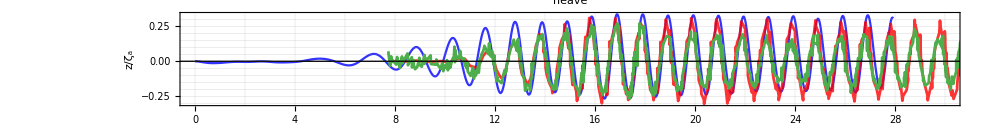

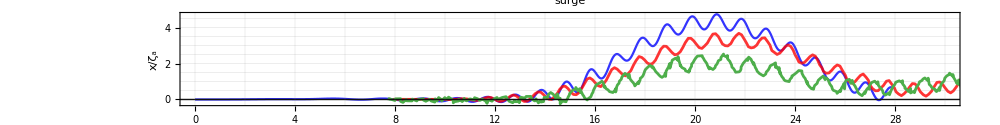

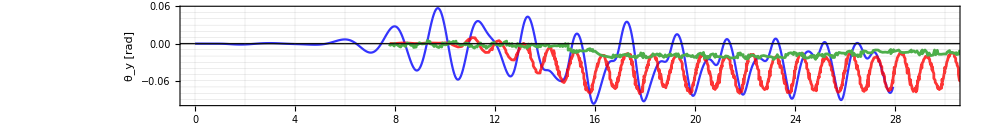

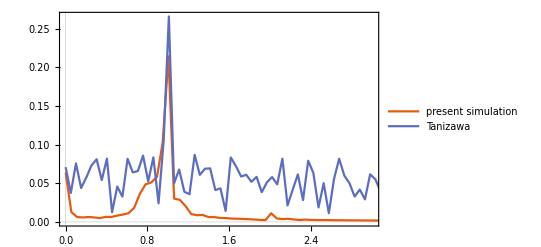

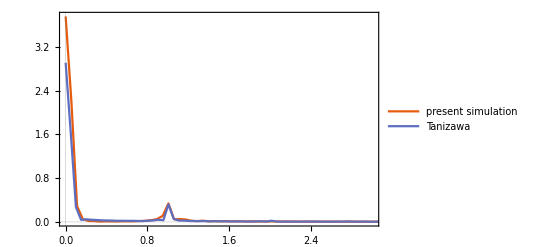

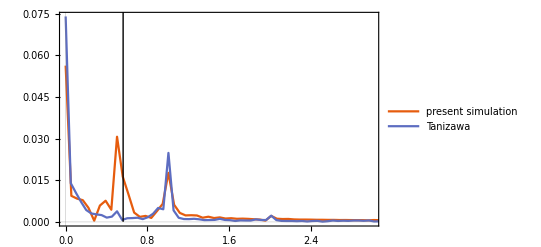

```mathematica
ListPlot[
{{importData[json,"simulation_time"]/Tw,(importData[json,"float_COM",3]-importData[json,"float_COM",3][[1]])/ζa}ᵀ,
SimuHeave,
ExpHeave},
Evaluate[opt],
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["z/ζ_a",FontSize->20,FontFamily->"Times"]},
PlotLabel->"heave",
Evaluate[plot2Doption]
]

ListPlot[
{{importData[json,"simulation_time"]/Tw,(importData[json,"float_COM",1]-importData[json,"float_COM",1][[1]])/ζa}ᵀ,
SimuSway,
ExpSway},
Evaluate[opt],
GridLines->{Table[i,{i,0.,6.,0.2}],Table[i,{i,-1.,1.,0.5}]},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x/ζ_a",FontSize->20,FontFamily->"Times"]},
PlotLabel->"surge",
Evaluate[plot2Doption]
]

k=2π/λ;
ListPlot[
{{importData[json,"simulation_time"]/Tw,-(importData[json,"float_pitch"])/(k*ζa)}ᵀ,
SimuRoll,
ExpRoll},
Evaluate[opt],
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["θ_y [rad]",FontSize->20,FontFamily->"Times"]},
Evaluate[plot2Doption]
]


ListPlot[
{interpolateAndFourier[importData[json,"simulation_time"]/Tw,(importData[json,"float_COM",3]-importData[json,"float_COM",3][[1]])/ζa,{10,30}],
interpolateAndFourierTr[SimuHeave,{10,30}]
},
PlotRange->{{0,3},All},
PlotLegends->{"present simulation","Tanizawa"},
Evaluate[plot2Doption]
]

ListPlot[
{interpolateAndFourier[importData[json,"simulation_time"]/Tw,(importData[json,"float_COM",1]-importData[json,"float_COM",1][[1]])/ζa,{10,30}],
interpolateAndFourierTr[SimuSway,{10,30}]
},
PlotRange->{{0,3},All},
PlotLegends->{"present simulation","Tanizawa"},
Evaluate[plot2Doption]
]

ListPlot[
{interpolateAndFourier[importData[json,"simulation_time"]/Tw,-(importData[json,"float_pitch"])/(k*ζa),{10,30}],
interpolateAndFourierTr[SimuRoll,{10,30}]
},
Epilog->Line[{{1/1.78,0},{1/1.78,10}}],
PlotRange->{{0,3},All},
PlotLegends->{"present simulation","Tanizawa"},
Evaluate[plot2Doption]
]
```

ロール角を除き，浮体の並進移動は，Tanizawa1997の計算結果とよく一致している．一方の回転角度は，谷澤の結果よりも小さく

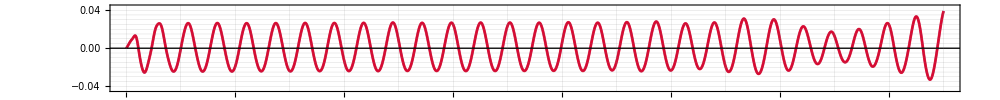
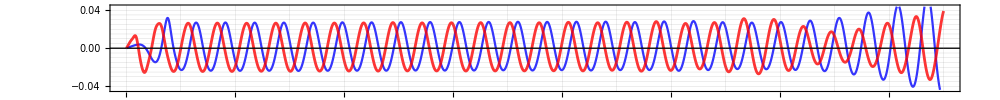
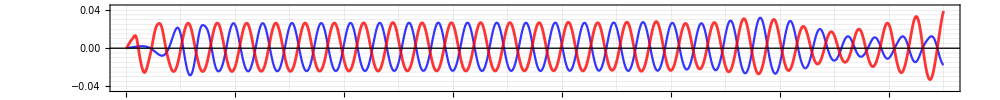
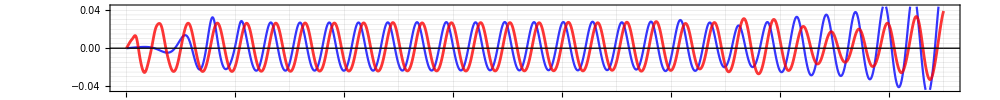
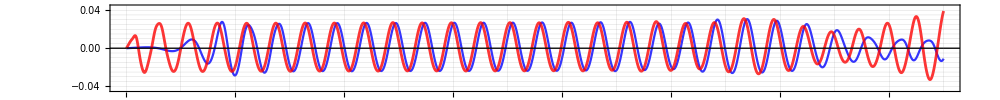
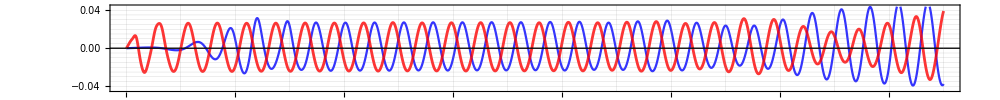
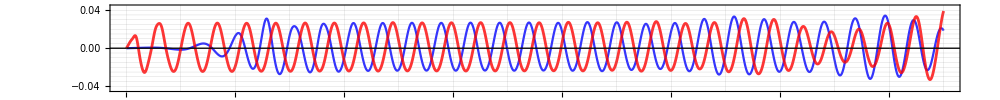
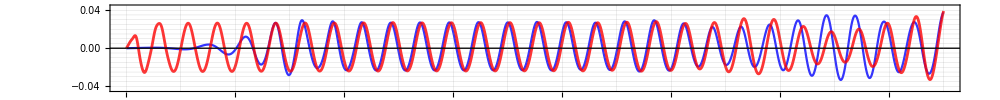
-Graphics-0.2
-Graphics-0.7
-Graphics-1.2
-Graphics-1.7
-Graphics-2.2
-Graphics-2.7
-Graphics-3.2
-Graphics-3.7
-Graphics-4.2
-Graphics-4.7
-Graphics-5.2
-Graphics-5.7
-Graphics-6.2
-Graphics-6.7
-Graphics-7.2
-Graphics-7.7
-Graphics-8.2
-Graphics-8.7
-Graphics-9.2
-Graphics-9.7
-Graphics-10.2
-Graphics-10.7
-Graphics-11.2
-Graphics-11.7

```mathematica
delt=0.67/(ω/k);
T=1.;
DATA1=importData[json,"gauge0_intersection",3];
Column[ParallelTable[
Module[{data,DATA,position},
data="gauge"<>ToString[i]<>"_intersection";
DATA=importData[json,data,3];
position=importData[json,data,1][[1]];
Labeled[
ListPlot[
{{importData[json,"simulation_time"],(DATA-DATA[[1]])}ᵀ,
{importData[json,"simulation_time"](*+(*0.295*)delt*i*),(DATA1-DATA1[[1]])}ᵀ
(*Table[{t,-ζa*Cos[2π/T*t-k*(position)]},{t,0,30,.1}]*)
},
(*FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x/H_0",FontSize->20,FontFamily->"Times",Italic]},*)
AspectRatio->1/10,
PlotRange->{Automatic,1.75*{-ζa,ζa}},
Joined->{True,True,True,True,True},
Evaluate[opt],
PlotStyle->plotstyle,
Evaluate[plot2Doption]
]
,position
,Right]
],{i,0,23,1}]
,Spacings->0
]
```

```mathematica
(*Mock-up for demonstration:Generates sample data similar to your structure*)
sampleData=ParallelTable[
Module[{data,DATA,position,w,v,fourier},
data="gauge"<>ToString[i]<>"_intersection";
DATA=importData[json,data,3];
position=importData[json,data,1][[1]];
{w,v}=Transpose[interpolateAndFourierTr[{importData[json,"simulation_time"],(DATA-DATA[[1]])}ᵀ,{10,15}]];
Transpose[{Table[i,{j,1,Length[w]}],w,v}]
],{i,1,20,1}];

minmax=MinMax[#3&@@@Flatten[sampleData,1]];

(*Visualization code*)
Graphics3D[Table[{ColorData["BlueGreenYellow"][sampleData[[i,j,3]]/minmax[[2]]],
Cuboid[{
sampleData[[i,j,1]],
sampleData[[i,j,2]],0},
{sampleData[[i,j,1]]+0.8,sampleData[[i,j,2]]+0.095,sampleData[[i,j,3]]}]},
{i,1,Length[sampleData]},{j,1,Length[sampleData[[i]]]}],Axes->True,BoxRatios->{1,1,1/2},PlotRange->{All,{0,3},All}]
```

-Graphics3D-

## 収束性のチェック

```mathematica
Clear["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../mathematica_utilities/mathematica_plot_options.nb"}]]
json="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json"
jsonInfo[json]
plotstyle=Table[RGBColor[{Sin[i*π]/2+1/2,Cos[i*π]/2+1/2,i}],{i,0,1,0.2}]
rbgs=Table["#"<>StringJoin[IntegerString[Round[#],16,2]&/@({255*Sin[i*π]/2+1/2,Cos[i*π]/2+1/2,i})],{i,0,1,0.2}]
hexColor="#"<>StringJoin[IntegerString[#,16,2]&/@rbgs[[1]]]


legend={(*"0.1",*)"0.09","0.08","0.07","0.06","0.05"}
```

Available:{plot2Doption,plot3Doption,framelabel[xlabel_String,ylabel_String,size_:20],axeslabel2D[xlabel_String,ylabel_String,size_:20],axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20],axeslabel[labels_List,size_: 20],importData,jsonInfo,interpolateAndFourier,interpolateAndFourierTr,getOmegaFromKandDepth,getTFromLandDepth}

/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.jsonが見付かりませんでした．

no. | title | length

{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]}

{#000100,#4b0100,#7a0100,#7a0001,#4b0001,#010001}

##000100

{0.09,0.08,0.07,0.06,0.05}

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Part::partw: (float_COM/.$Failed)⟦1;;All,3⟧の部分250は存在しません．

Transpose::nmtx: {simulation_time/.$Failed,-(float_COM/.$Failed)⟦1;;All,3⟧⟦250⟧+(float_COM/.$Failed)⟦1;;All,3⟧}の最初の2個のレベルは転置できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

Part::partw: (float_COM/.$Failed)⟦1;;All,3⟧の部分250は存在しません．

Transpose::nmtx: {simulation_time/.$Failed,-(float_COM/.$Failed)⟦1;;All,3⟧⟦250⟧+(float_COM/.$Failed)⟦1;;All,3⟧}の最初の2個のレベルは転置できません．

Part::partw: (float_COM/.$Failed)⟦1;;All,3⟧の部分250は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

Transpose::nmtx: {simulation_time/.$Failed,-(float_COM/.$Failed)⟦1;;All,3⟧⟦250⟧+(float_COM/.$Failed)⟦1;;All,3⟧}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

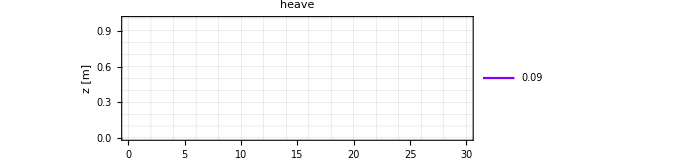

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

Part::partw: (float_COM/.$Failed)⟦1;;All,1⟧の部分250は存在しません．

Transpose::nmtx: {simulation_time/.$Failed,-(float_COM/.$Failed)⟦1;;All,1⟧⟦250⟧+(float_COM/.$Failed)⟦1;;All,1⟧}の最初の2個のレベルは転置できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

Part::partw: (float_COM/.$Failed)⟦1;;All,1⟧の部分250は存在しません．

Transpose::nmtx: {simulation_time/.$Failed,-(float_COM/.$Failed)⟦1;;All,1⟧⟦250⟧+(float_COM/.$Failed)⟦1;;All,1⟧}の最初の2個のレベルは転置できません．

Part::partw: (float_COM/.$Failed)⟦1;;All,1⟧の部分250は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

Transpose::nmtx: {simulation_time/.$Failed,-(float_COM/.$Failed)⟦1;;All,1⟧⟦250⟧+(float_COM/.$Failed)⟦1;;All,1⟧}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

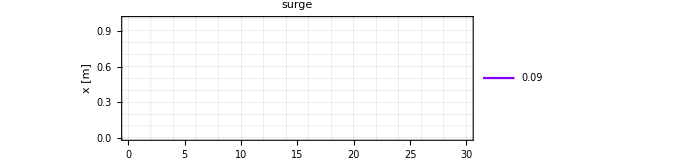

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partw: float_pitch/.$Failedの部分250は存在しません．

Transpose::nmtx: {simulation_time/.$Failed,(float_pitch/.$Failed)⟦250⟧-(float_pitch/.$Failed)}の最初の2個のレベルは転置できません．

Part::partw: float_pitch/.$Failedの部分250は存在しません．

Transpose::nmtx: {simulation_time/.$Failed,(float_pitch/.$Failed)⟦250⟧-(float_pitch/.$Failed)}の最初の2個のレベルは転置できません．

Part::partw: float_pitch/.$Failedの部分250は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

Transpose::nmtx: {simulation_time/.$Failed,(float_pitch/.$Failed)⟦250⟧-(float_pitch/.$Failed)}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

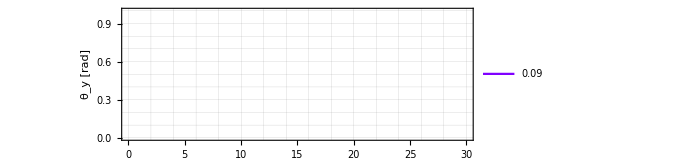

```mathematica
jsons={(*"/Volumes/home/BEM/20240301土木学会東北支部/Tanizawa1996_H0d05_L1d8_potential_water_mod_0d1/result.json",*)
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d08/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d07/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d05/result.json"(*,
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_3/result.json"*)};

plotxrange={{0,30},All};
opt2={FrameStyle->Directive[FontSize->16,Black,Thickness[0.002]],
PlotStyle->plotstyle,
Joined->{True,True,True,True},
PlotRange->plotxrange,
GridLines->All,
GridLinesStyle->Directive[Gray,AbsoluteThickness[0.001]],
ImageSize->500,
(*PlotStyle->{{Darker[Blue,0.1]},{Darker[Blue,0.3]},{Darker[Blue,0.6]},{Darker[Blue,0.9]}},*)
AspectRatio->1/3};
(*メッシュと計算の収束*)

fig=ListPlot[
Table[{importData[jsons[[i]],"simulation_time"],(importData[jsons[[i]],"float_COM",3]-importData[jsons[[i]],"float_COM",3][[250]])}ᵀ,
{i,1,Length[jsons]}],
PlotStyle->plotstyle,
Evaluate[opt2],
(*PlotRange->{{0,12.},{-0.07,0.07}},*)
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["z [m]",FontSize->20,FontFamily->"Times"]},
PlotLegends->legend,
PlotLabel->"heave",
Evaluate[plot2Doption]
]
ListPlot[
Table[{importData[jsons[[i]],"simulation_time"],(importData[jsons[[i]],"float_COM",1]-importData[jsons[[i]],"float_COM",1][[250]])}ᵀ,{i,1,Length[jsons]}],
PlotStyle->plotstyle,
Evaluate[opt2],
PlotRange->{All,Automatic},
GridLines->{Table[i,{i,0.,6.,0.2}],Table[i,{i,-1.,1.,0.5}]},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x [m]",FontSize->20,FontFamily->"Times"]},
PlotLegends->legend,
PlotLabel->"surge",
Evaluate[plot2Doption]
]
k=2π/λ;
ListPlot[
Table[{importData[jsons[[i]],"simulation_time"],-(importData[jsons[[i]],"float_pitch"]-importData[jsons[[i]],"float_pitch"][[250]])}ᵀ,{i,1,Length[jsons]}],
PlotStyle->plotstyle,
Evaluate[opt2],
PlotLegends->legend,
PlotRange->{All,All},
PlotRange->{Automatic,Automatic},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["θ_y [rad]",FontSize->20,FontFamily->"Times"]},
Evaluate[plot2Doption]
]
```

```mathematica
json1="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water_no_float0d09/result.json"
delt=0.67/(ω/k);
T=1.;
DATA1=importData[json1,"gauge0_intersection",3];
Column[ParallelTable[
Module[{data,DATA,position},
data="gauge"<>ToString[i]<>"_intersection";
DATA=importData[json,data,3];
position=importData[json,data,1][[1]];
Labeled[
ListPlot[
{{importData[json,"simulation_time"],(DATA-DATA[[1]])}ᵀ,
{importData[json,"simulation_time"](*+(*0.295*)delt*i*),(DATA1-DATA1[[1]])}ᵀ
(*Table[{t,-ζa*Cos[2π/T*t-k*(position)]},{t,0,30,.1}]*)
},
(*FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x/H_0",FontSize->20,FontFamily->"Times",Italic]},*)
AspectRatio->1/10,
PlotRange->{Automatic,1.75*{-ζa,ζa}},
Joined->{True,True,True,True,True},
Evaluate[opt],
PlotStyle->plotstyle,
Evaluate[plot2Doption]
]
,position
,Right]
],{i,0,23,1}]
,Spacings->0
]
```

/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water_no_float0d09/result.json

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water_no_float0d09/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(gauge0_intersection/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Import::nffil: File /Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json not found during Import.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification (gauge0_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge2_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge4_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge6_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge8_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge10_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge12_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge14_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge16_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge17_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge18_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge19_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge20_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge21_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge22_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge23_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Import::nffil: File /Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json not found during Import.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification (gauge0_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge2_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge4_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge6_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge8_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge10_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge12_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge14_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge16_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge17_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge18_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge19_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge20_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge21_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge22_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge23_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Import::nffil: File /Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge2_intersection/.$Failed)⟦1;;All,3⟧-(gauge2_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge4_intersection/.$Failed)⟦1;;All,3⟧-(gauge4_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge6_intersection/.$Failed)⟦1;;All,3⟧-(gauge6_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge8_intersection/.$Failed)⟦1;;All,3⟧-(gauge8_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge10_intersection/.$Failed)⟦1;;All,3⟧-(gauge10_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge12_intersection/.$Failed)⟦1;;All,3⟧-(gauge12_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge14_intersection/.$Failed)⟦1;;All,3⟧-(gauge14_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge16_intersection/.$Failed)⟦1;;All,3⟧-(gauge16_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge17_intersection/.$Failed)⟦1;;All,3⟧-(gauge17_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge18_intersection/.$Failed)⟦1;;All,3⟧-(gauge18_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge19_intersection/.$Failed)⟦1;;All,3⟧-(gauge19_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge20_intersection/.$Failed)⟦1;;All,3⟧-(gauge20_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge21_intersection/.$Failed)⟦1;;All,3⟧-(gauge21_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge22_intersection/.$Failed)⟦1;;All,3⟧-(gauge22_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge23_intersection/.$Failed)⟦1;;All,3⟧-(gauge23_intersection/.$Failed)} cannot be transposed.

Part::partd: Part specification (gauge0_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)} cannot be transposed.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in …. An option must be a rule or a list of rules.

General::stop: Further output of ListPlot::nonopt will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge1_intersection/.$Failed)⟦1;;All,3⟧-(gauge1_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge3_intersection/.$Failed)⟦1;;All,3⟧-(gauge3_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge5_intersection/.$Failed)⟦1;;All,3⟧-(gauge5_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge7_intersection/.$Failed)⟦1;;All,3⟧-(gauge7_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge9_intersection/.$Failed)⟦1;;All,3⟧-(gauge9_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge11_intersection/.$Failed)⟦1;;All,3⟧-(gauge11_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge13_intersection/.$Failed)⟦1;;All,3⟧-(gauge13_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge15_intersection/.$Failed)⟦1;;All,3⟧-(gauge15_intersection/.$Failed)} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(gauge0_intersection/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Transpose::nmtx: {simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}の最初の2個のレベルは転置できません．

Part::partd: 部分指定(gauge0_intersection/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Transpose::nmtx: {simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}の最初の2個のレベルは転置できません．

ListPlot::nonopt: …における1の位置より後方にオプションが想定されます（optの代りに）．オプションは規則あるいは規則のリストでなければなりません．

General::stop: この計算中に，ListPlot::nonoptのこれ以上の出力は表示されません．

Part::partd: 部分指定(gauge1_intersection/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

Transpose::nmtx: {simulation_time/.$Failed,(gauge1_intersection/.$Failed)⟦1;;All,3⟧-(gauge1_intersection/.$Failed)}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

ListPlot[{Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge0_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge1_intersection/.$Failed)⟦1;;All,3⟧-(gauge1_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge1_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge2_intersection/.$Failed)⟦1;;All,3⟧-(gauge2_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge2_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge3_intersection/.$Failed)⟦1;;All,3⟧-(gauge3_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge3_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge4_intersection/.$Failed)⟦1;;All,3⟧-(gauge4_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge4_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge5_intersection/.$Failed)⟦1;;All,3⟧-(gauge5_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge5_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge6_intersection/.$Failed)⟦1;;All,3⟧-(gauge6_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge6_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge7_intersection/.$Failed)⟦1;;All,3⟧-(gauge7_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge7_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge8_intersection/.$Failed)⟦1;;All,3⟧-(gauge8_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge8_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge9_intersection/.$Failed)⟦1;;All,3⟧-(gauge9_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge9_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge10_intersection/.$Failed)⟦1;;All,3⟧-(gauge10_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge10_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge11_intersection/.$Failed)⟦1;;All,3⟧-(gauge11_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge11_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge12_intersection/.$Failed)⟦1;;All,3⟧-(gauge12_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge12_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge13_intersection/.$Failed)⟦1;;All,3⟧-(gauge13_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge13_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge14_intersection/.$Failed)⟦1;;All,3⟧-(gauge14_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge14_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge15_intersection/.$Failed)⟦1;;All,3⟧-(gauge15_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge15_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge16_intersection/.$Failed)⟦1;;All,3⟧-(gauge16_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge16_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge17_intersection/.$Failed)⟦1;;All,3⟧-(gauge17_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge17_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge18_intersection/.$Failed)⟦1;;All,3⟧-(gauge18_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge18_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge19_intersection/.$Failed)⟦1;;All,3⟧-(gauge19_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge19_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge20_intersection/.$Failed)⟦1;;All,3⟧-(gauge20_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge20_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge21_intersection/.$Failed)⟦1;;All,3⟧-(gauge21_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge21_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge22_intersection/.$Failed)⟦1;;All,3⟧-(gauge22_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge22_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge23_intersection/.$Failed)⟦1;;All,3⟧-(gauge23_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge23_intersection/.$Failed

## 伝播の収束のチェック

```mathematica
Clear["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../mathematica_utilities/mathematica_plot_options.nb"}]]
(*start=18.15;
end=30;*)
start=0;
end=30;
```

Available:{plot2Doption,plot3Doption,framelabel[xlabel_String,ylabel_String,size_:20],axeslabel2D[xlabel_String,ylabel_String,size_:20],axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20],axeslabel[labels_List,size_: 20],importData,jsonInfo,interpolateAndFourier,interpolateAndFourierTr,getOmegaFromKandDepth,getTFromLandDepth}

```mathematica
importData[filename_String,var_,n_: 0,replacement_: Missing[]]:=Module[{imported=Import[filename],processed},processed=imported/.{"NaN"|"Nan"|"null"|"nan"|Null->replacement};
If[n>0,(var/.processed)[[;;,n]],var/.processed]];

fileDir="/Volumes/home/BEM/benchmark202405";
(*fileDir="/Users/tomoaki/BEM";*)
```

```mathematica
jsons={
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMlinear_ALEpseudo_quad","Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMpseudo_quad_ALEpseudo_quad",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALEpseudo_quad","Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMpseudo_quad_ALEpseudo_quad",
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMlinear_ALEpseudo_quad","Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMpseudo_quad_ALElinear","Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMpseudo_quad_ALEpseudo_quad","Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMlinear_ALElinear",
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALEpseudo_quad","Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMpseudo_quad_ALElinear","Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMpseudo_quad_ALEpseudo_quad"};
jsons=FileNameJoin[{fileDir,#,"result.json"}]&/@jsons;
```

```mathematica
ExtractInfoFromPath[path_String]:=Module[{splitPath,mesh,h,dt,elementBVPandIVP,elementALE,ALEperiod},splitPath=StringSplit[path,{"_","/"}];
(*Hの値を抽出*)
h=SelectFirst[splitPath,StringContainsQ[#,"H0d"]&];
h=StringReplace[h,{"H0d"->"H=0."}];

(*dtの値を抽出*)
dt=SelectFirst[splitPath,StringContainsQ[#,"DT0d"]&];
dt=StringReplace[dt,{"DT0d"->"dt=0."}];

(*meshの値を抽出*)
mesh=SelectFirst[splitPath,StringContainsQ[#,"float0d"]&];
mesh=StringReplace[mesh,{"float0d"->"dl=0."}];

(*BVPとIVPのための要素を抽出*)
elementBVPandIVP=SelectFirst[splitPath,StringContainsQ[#,"ELEM"]&];
elementBVPandIVP=StringReplace[elementBVPandIVP,"ELEM"->"BVP:"];

(*ALEの要素を抽出*)
elementALE=SelectFirst[splitPath,StringContainsQ[#,"ALE"]&];
elementALE=StringReplace[elementALE,"ALE"->"ALE:"];

(*ALE periodの値を抽出*)
ALEperiod=SelectFirst[splitPath,StringContainsQ[#,"ALEPERIOD"]&,"ALEPERIOD1"];
ALEperiod=StringReplace[ALEperiod,{"ALEPERIOD"->"ALE Step Period:"}];


(*結果を返す*)
{mesh,h,dt,elementBVPandIVP,elementALE,ALEperiod}];

(*gauges={"gauge2_intersection","gauge22_intersection"};*)
(*gauges={"gauge4_intersection","gauge23_intersection"};*)
gauges={"gauge2_intersection","gauge22_intersection"};
colors={Blue,Red,Darker[Green],Black};
(*---------------------------------------------*)
compare[jsons_,zrange_:(5+{-0.06,0.06}),surface_:5]:=Module[{size,ratio,h,legend},
size=700;
ratio=1/5;
h=surface;

select[json_,name_]:=Module[{data},
Select[Transpose[{importData[json,"simulation_time"],importData[json,name,3]}],start≤#[[1]]≤end&]
];

selectAndNegateMean[json_,name_]:=Module[{data},
data=Select[Transpose[{importData[json,"simulation_time"],importData[json,name,3]}],start≤#[[1]]≤end&];
mean=Mean[Transpose[data][[2]]];
{#1,#2-mean}&@@@data
];
(*colors={Blue,Orange,Green,Magenta};*)

(*colors={RGBColor[0.4,0.7,0.9],(*Sky Blue*)RGBColor[0.9,0.6,0.0],(*Soft Orange*)RGBColor[0.5,0.3,0.7],(*Plum Purple*)RGBColor[0.3,0.7,0.0]  (*Apple Green*)};*)



legend=LineLegend[colors[[;;Length[jsons]]],StringJoin [Riffle[ExtractInfoFromPath[#],", "]]&/@jsons,
LegendMarkerSize->{{40,5}},
LabelStyle->{FontFamily->"Times",FontSize->15},
LegendLayout->"Row",
LegendFunction->"Frame"];
(*=======================================================================*)
Grid[
{{legend,SpanFromLeft},
{
Labeled[Column[Table[ListPlot[
Table[select[json,name],{json,jsons}]
,PlotRange->{All,h+zrange}
,PlotStyle->colors
,GridLines->Automatic
,AspectRatio->ratio
,ImageSize->size
(*,Epilog->{{Dashed,Line[{{start,h+0.05},{end,h+0.05}}]},{Dashed,Line[{{start,h-0.05},{end,h-0.05}}]}}*)
,Epilog->Inset[Framed[Style["d="<>ToString@importData[jsons[[1]],name,1][[1]]<>" m",10],Background->LightYellow],Scaled[{0.925,0.15}]]
,Joined->True
,BaseStyle->Directive[FontFamily->"Times New Roman",FontSize->16]
,Evaluate[plot2Doption]],
{name,gauges}]]
,framelabel["Time [s]","Surface Elevation [m]",16,{0,Pi/2}],{Bottom,Left}
,ImageMargins->{{10,0},{0,0}}
]
},
{
Labeled[
Row[Table[ListStepPlot[Table[{#1,#2}&@@@(interpolateAndFourier[#1,#2]&@@Transpose[selectAndNegateMean[json,name]]),{json,jsons}]
,Center
,PlotStyle->colors
,GridLines->Automatic
,AspectRatio->ratio*2.
,ImageSize->size/2.
,Epilog->Inset[Framed[Style["d="<>ToString@importData[jsons[[1]],name,1][[1]]<>" m",10],Background->LightYellow],Scaled[{0.85,0.85}]]
,PlotRange->{{0.,3},{All,zrange[[2]]}(*,{0,0.026}*)}
,Joined->False
,Filling->Bottom
,BaseStyle->Directive[FontFamily->"Times New Roman",FontSize->16]
,Evaluate[plot2Doption]
],
{name,gauges}]]
,framelabel["Frequency [s^-1]","Amplitude.08 [m]",16,{0,Pi/2}],{Bottom,Left}
,ImageMargins->{{10,0},{0,0}}
]
}
}
]
]
(*=======================================================================*)
compareSimple[jsons_,zrange_:(5+{-0.06,0.06}),surface_:5]:=Module[{size,ratio,h,legend},
size=700;
ratio=1/5;
h=surface;

select[json_,name_]:=Module[{data},
Select[Transpose[{importData[json,"simulation_time"],importData[json,name,3]}],start≤#[[1]]≤end&]
];

selectAndNegateMean[json_,name_]:=Module[{data},
data=Select[Transpose[{importData[json,"simulation_time"],importData[json,name,3]}],start≤#[[1]]≤end&];
mean=Mean[Transpose[data][[2]]];
{#1,#2-mean}&@@@data
];
(*colors={Blue,Orange,Green,Magenta};*)

(*colors={RGBColor[0.4,0.7,0.9],(*Sky Blue*)RGBColor[0.9,0.6,0.0],(*Soft Orange*)RGBColor[0.5,0.3,0.7],(*Plum Purple*)RGBColor[0.3,0.7,0.0]  (*Apple Green*)};*)

legend=LineLegend[colors[[;;Length[jsons]]],StringJoin [Riffle[ExtractInfoFromPath[#],", "]]&/@jsons,
LegendMarkerSize->{{40,5}},
LabelStyle->{FontFamily->"Times",FontSize->15},
LegendLayout->"Row",
LegendFunction->"Frame"];

Grid[
{{legend,SpanFromLeft},
{
Labeled[Column[Table[ListPlot[
Table[select[json,name],{json,jsons}]
,PlotRange->{All,h+zrange}
,PlotStyle->colors
,GridLines->Automatic
,AspectRatio->ratio/1.5
,ImageSize->size
(*,Epilog->{{Dashed,Line[{{start,h+0.05},{end,h+0.05}}]},{Dashed,Line[{{start,h-0.05},{end,h-0.05}}]}}*)
,Epilog->Inset[Framed[Style["d="<>ToString@importData[jsons[[1]],name,1][[1]]<>" m",10],Background->LightYellow],Scaled[{0.05,0.15}]]
,Joined->True
,BaseStyle->Directive[FontFamily->"Times New Roman",FontSize->16]
,Evaluate[plot2Doption]],
{name,{
"gauge2_intersection",
"gauge7_intersection",
"gauge12_intersection",
"gauge17_intersection",
"gauge22_intersection"}}]]
,framelabel["Time [s]","Surface Elevation [m]",16,{0,Pi/2}],{Bottom,Left}
,ImageMargins->{{10,0},{0,0}}
]
}
}
,Spacings->0]
]
(*=======================================================================*)
fileName[{H_,L_,WAVE_,MESH_,DT_,ELEM_,ALE_}]:=Module[{formatNumber},
formatNumber[n_]:=StringReplace[ToString[N[n]],"."->"d"];
StringJoin["Tanizawa1996_",
"H",formatNumber[H],
"_L",formatNumber[L],
"_WAVE",WAVE,
"_MESH",MESH,
"_DT",formatNumber[DT],
"_ELEM",ELEM,
"_ALE",ALE]]
```

```mathematica
(*gaugeのx座標*)
FileNameJoin[{fileDir,fileName[{0.1,1.8,"potential","water_no_float0d08",0.05,"linear","linear"}],"result.json"}]
importData[FileNameJoin[{fileDir,fileName[{0.1,1.8,"potential","water_no_float0d08",0.05,"linear","linear"}],"result.json"}],gauges[[2]],1][[1]]
importData[FileNameJoin[{fileDir,fileName[{0.1,1.8,"potential","water_no_float0d08",0.05,"linear","linear"}],"result.json"}],gauges[[1]],1][[1]]
```

/Volumes/home/BEM/benchmark202405/Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALElinear/result.json

Import::nffil: Importの最中にファイル/Volumes/home/BEM/benchmark202405/Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALElinear/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(gauge22_intersection/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

gauge22_intersection/.$Failed

Import::nffil: Importの最中にファイル/Volumes/home/BEM/benchmark202405/Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALElinear/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(gauge2_intersection/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

gauge2_intersection/.$Failed

```mathematica
(*少しチェック*)
F=getOmegaFromLandDepth[1.8,50.]/(2*π)
T=1/F
```

0.93134

1.07372

```mathematica
2*π/getOmegaFromLandDepth[1.8,5.]
```

1.07372

#### 減衰へのALE毎回．meshの細かさの影響（おいおい）

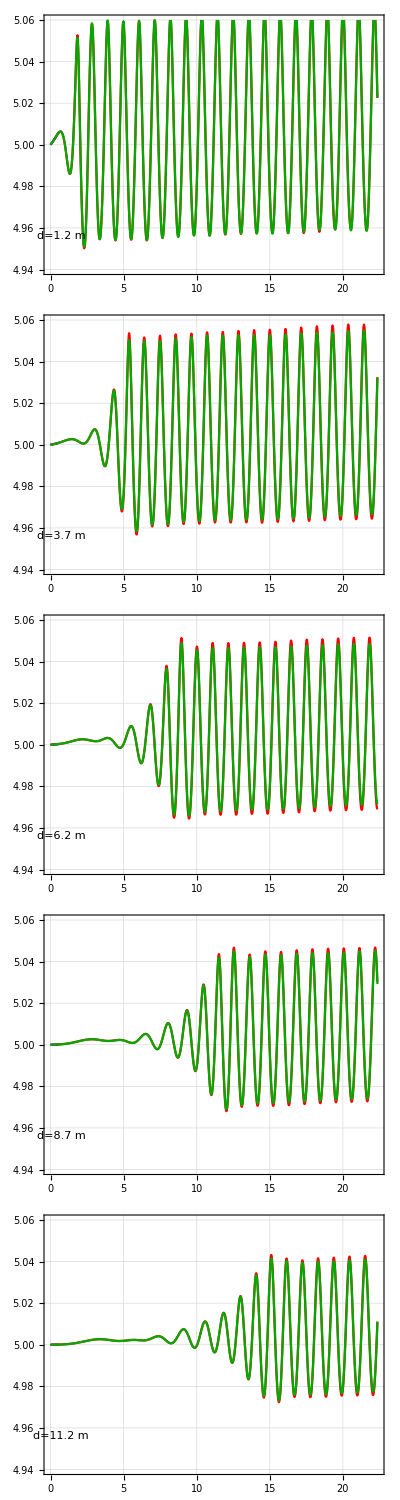
| 
-Graphics-Time [s]Surface Elevation [m] |

/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/mesh_quality_ELEMlinear_ALElinear_H0d1.png

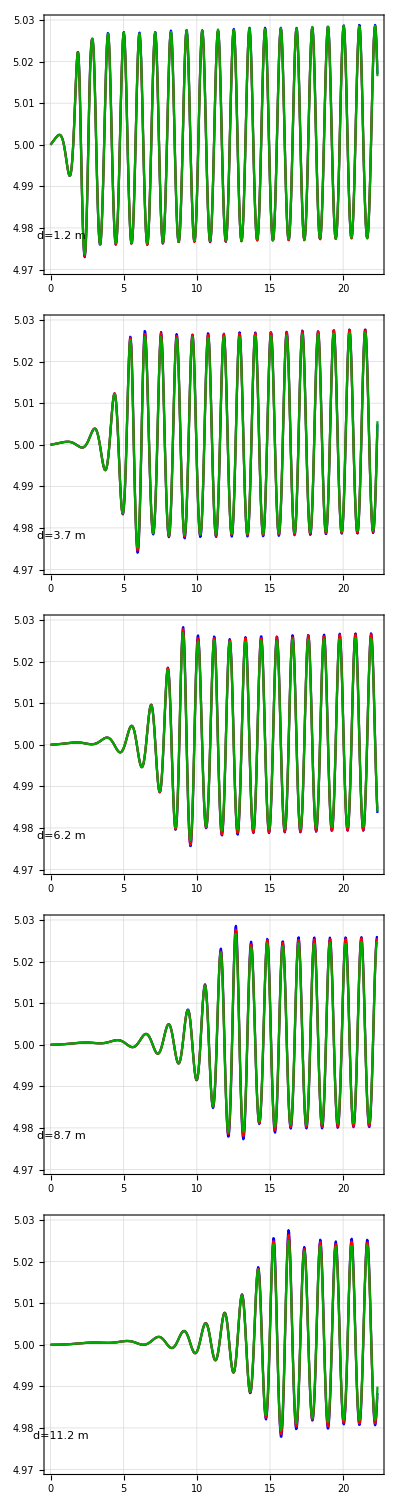
| 
-Graphics-Time [s]Surface Elevation [m] |

/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/mesh_quality_ELEMlinear_ALElinear_H0d05.png

ALEの頻度を1/3にすると，波の減衰が大幅に抑えられた．

```mathematica
zrange={-0.06,0.06};
{start,end}={0.,17.+T*5};

ALE="linear";
(*comp0d07={fileName[{0.1,1.8,"potential","water_no_float0d07",0.05,"linear",ALE}],
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD3"};
*)
comp0d08={
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d06_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1"};
fig=compareSimple[FileNameJoin[{fileDir,#,"result.json"}]&/@comp0d08,zrange]
Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/mesh_quality_ELEMlinear_ALElinear_H0d1.png",fig,ImageResolution->300]

comp0d08={
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d06_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1"};

fig=compareSimple[FileNameJoin[{fileDir,#,"result.json"}]&/@comp0d08,{-0.03,0.03}]

Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/mesh_quality_ELEMlinear_ALElinear_H0d05.png",fig,ImageResolution->300]

Text["ALEの頻度を1/3にすると，波の減衰が大幅に抑えられた．"]
```

#### 減衰へのALE頻度の影響 ALE:linear

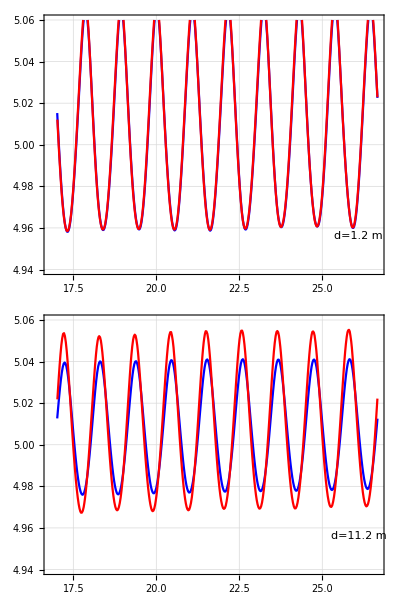
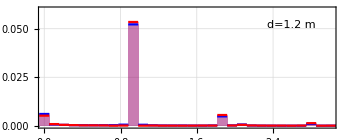
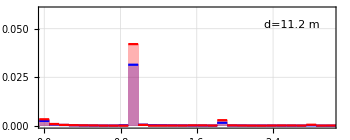
| 
-Graphics-Time [s]Surface Elevation [m] | 
-Graphics--Graphics-Frequency [s^-1]Amplitude.08 [m] |

$Failed

ALEの頻度を1/3にすると，波の減衰が大幅に抑えられた．

```mathematica
zrange={-0.03,0.03}*2;
{start,end}={17.,17.+T*9};

ALE="linear";
(*comp0d07={fileName[{0.1,1.8,"potential","water_no_float0d07",0.05,"linear",ALE}],
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD3"};
*)
comp0d08={
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD3"};

fig=compare[FileNameJoin[{fileDir,#,"result.json"}]&/@comp0d08,zrange]

Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/dl0d08_ALE_frequency_comparison.png",fig,ImageResolution->225]

Text["ALEの頻度を1/3にすると，波の減衰が大幅に抑えられた．"]
```

#### 減衰へのALE頻度の影響 ALE:pseudo-quad

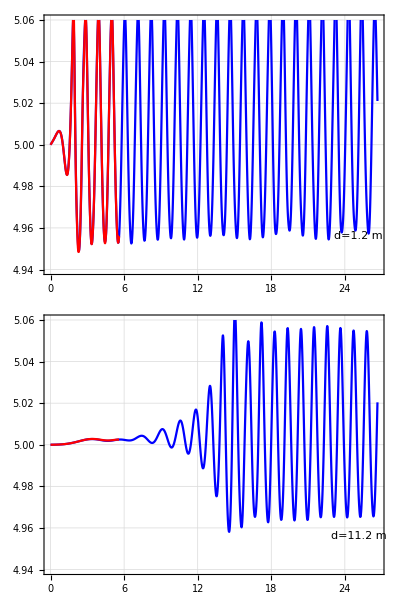
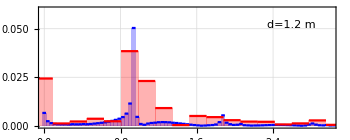
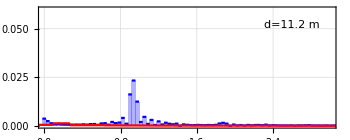
| 
-Graphics-Time [s]Surface Elevation [m] | 
-Graphics--Graphics-Frequency [s^-1]Amplitude.08 [m] |

$Failed

ALEがpseudoの場合でも頻度を1/3にすると，波の減衰が大幅に抑えられた．ただし，ALEがlinearの場合よりもALE pseudo quadは減衰が生じにくい．

```mathematica
zrange={-0.03,0.03}*2;
{start,end}={0.,17.+T*9};
ALE="pseudo_quad";
(*comp0d07={fileName[{0.1,1.8,"potential","water_no_float0d07",0.05,"linear",ALE}],
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD3"};*)

comp0d08={
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD3"};


fig=compare[FileNameJoin[{fileDir,#,"result.json"}]&/@comp0d08,zrange]

Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/dl0d08_ALE_frequency_pseudo_comparison.png",fig,ImageResolution->225]

Text["ALEがpseudoの場合でも頻度を1/3にすると，波の減衰が大幅に抑えられた．ただし，ALEがlinearの場合よりもALE pseudo quadは減衰が生じにくい．"]
```

#### BVPに擬2次要素を使った場合

```mathematica
zrange={-0.03,0.03}*2.;
colors=RotateLeft[colors,2];
ALE="pseudo_quad";
BVP="linear";
comp={
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMpseudo_quad_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1"}

compare[FileNameJoin[{fileDir,#,"result.json"}]&/@comp,zrange]

Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/MESH0d08_ELEMpseudo_quad_H0d1.png",%,ImageResolution->225]

Text["ALEを頻繁にメッシュに適用してメッシュを均一にしなければ，pseudo-quadの精度は悪化し，計算が破綻してしまうようだ．
pseudo-quadは，歪なメッシュにおいては計算が不安定になる可能性がある．"]
```

{Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1,Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALEpseudo_quad_ALEPERIOD1}

$Failed

ALEを頻繁にメッシュに適用してメッシュを均一にしなければ，pseudo-quadの精度は悪化し，計算が破綻してしまうようだ．
pseudo-quadは，歪なメッシュにおいては計算が不安定になる可能性がある．

#### 最も良いと思われる計算

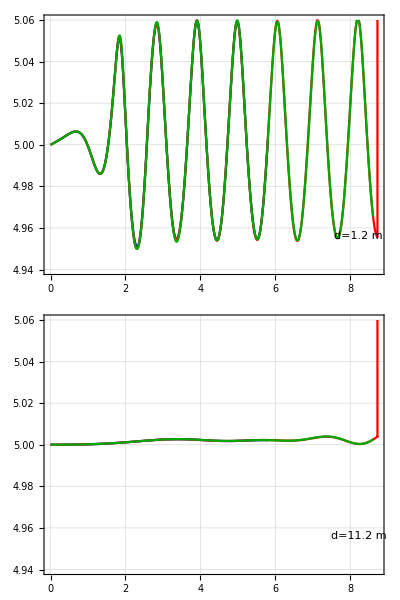
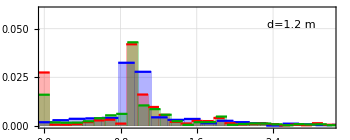
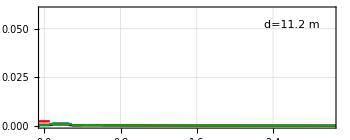
| 
-Graphics-Time [s]Surface Elevation [m] | 
-Graphics--Graphics-Frequency [s^-1]Amplitude.08 [m] |

ALEがpseudoの場合でも頻度を1/3にすると，波の減衰が大幅に抑えられた．ただし，ALEがlinearの場合よりもALE pseudo quadは減衰が生じにくい．

```mathematica
zrange={-0.03,0.03}*2;
{start,end}={0.,T*14};
ALE="pseudo_quad";
fileDir="/Volumes/home/BEM/benchmark202405";
(*comp0d07={fileName[{0.1,1.8,"potential","water_no_float0d07",0.05,"linear",ALE}],
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD3"};*)

comp0d08={
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALElinear_ALEPERIOD1",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALElinear_ALEPERIOD1",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d06_DT0d05_ELEMlinear_ALElinear_ALEPERIOD1"};


fig=compare[FileNameJoin[{fileDir,#,"result.json"}]&/@comp0d08,zrange]

(*Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/dl0d08_ALE_frequency_pseudo_comparison.png",fig,ImageResolution->225]
*)
Text["ALEがpseudoの場合でも頻度を1/3にすると，波の減衰が大幅に抑えられた．ただし，ALEがlinearの場合よりもALE pseudo quadは減衰が生じにくい．"]
```

{141.12,152.64,190.08,204.48}

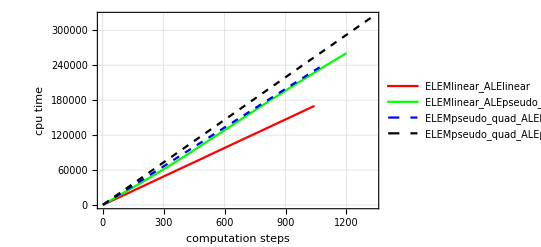

{141.12,152.64,190.08,204.48}

{1.,1.08163,1.34694,1.44898}

```mathematica
list={
"ELEMlinear_ALElinear",
"ELEMlinear_ALEpseudo_quad",
"ELEMpseudo_quad_ALElinear",
"ELEMpseudo_quad_ALEpseudo_quad"};
(*clist={5000,6000,7000,8000}*0.96;*)
clist={4900,5300,6600,7100}*0.96*0.03
Show[ListPlot[
Table[importData["/Volumes/home/BEM/benchmark202404/Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_"<>name<>"/result.json","cpu_time"]
(*}*)
,{name,list}]
,FrameLabel->framelabel["computation steps","cpu time"]
,PlotStyle->{Red,{Green},{Blue,Dashed},{Black,Dashed}}
,PlotLegends->list
,GridLines->Automatic
(*,PlotRange->{{0,10},Automatic}*)
,Evaluate[plot2Doption]]
(*,
Plot[Table[c*x,{c,clist}],{x,0,10}]*)
]

clist
clist/clist[[1]]
```